Numero de supernovas: 580

=== Primeros 10 valores de μ teorico (w = -1.0) ===

z | μ
0.001 | 28.1603
0.002 | 29.6671
0.003 | 30.5493
0.004 | 31.1756
0.005 | 31.6618
0.006 | 32.0594
0.007 | 32.3958
0.008 | 32.6874
0.009 | 32.9449
0.01 | 33.1753

Part::pkspec1: The expression i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

=== Figura 1: Curvas teoricas (eje x log) ===

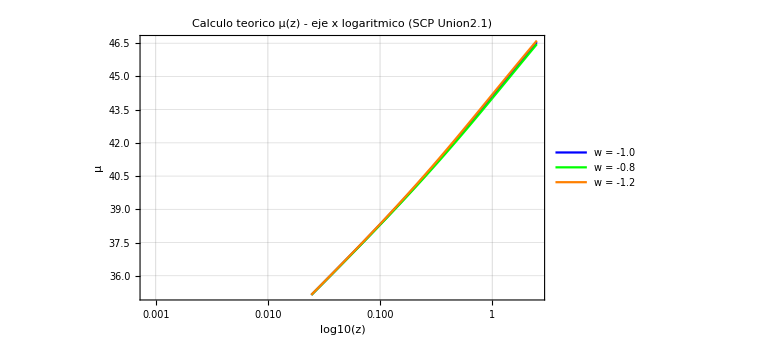

=== Figura 2: Datos con barras de error (eje x log) ===

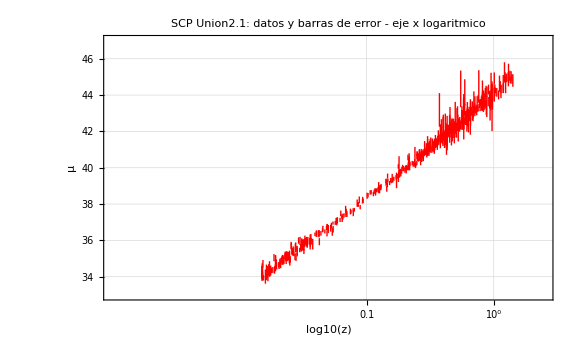

=== Figura 3: Superposicion teoria + datos (eje x log) ===

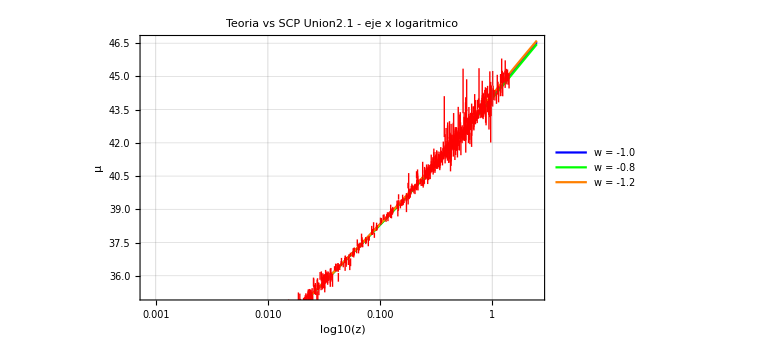

Part::pkspec1: The expression i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

=== Figura 4: Curvas teoricas (ambos ejes log) ===

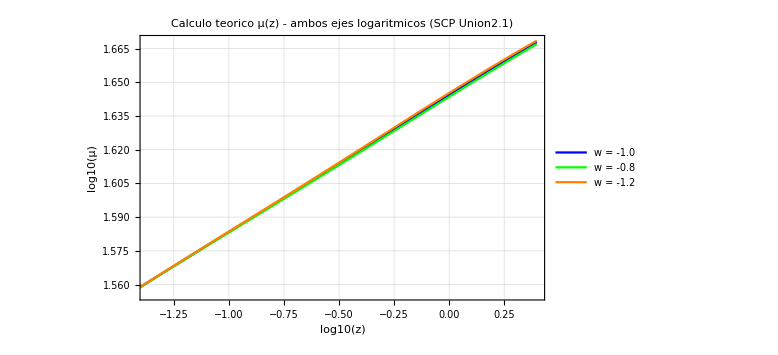

=== Figura 5: Datos con barras de error (ambos ejes log) ===

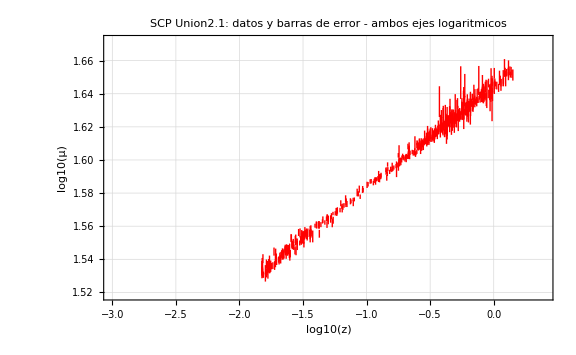

=== Figura 6: Superposicion teoria + datos (ambos ejes log) ===

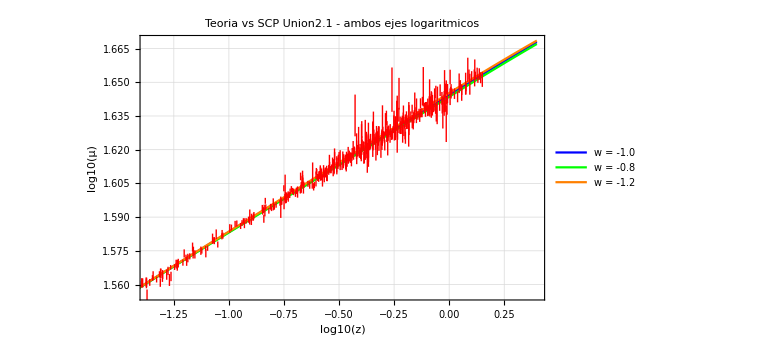

=== Chi cuadrado para w fijo ===

Chi2 (w = -1.0) = 565.003

Chi2 (w = -0.8) = 630.056

Chi2 (w = -1.2) = 582.156

Calculando chi cuadrado en bucle 2D...

Minimo global: χ^2 = 562.227 en OmegaM = 0.278, w = -1., OmegaDE = 0.722

Puntos dentro de 1σ: 182

Puntos dentro de 2σ: 377

Puntos dentro de 3σ: 550

=== Figura 7: Contour plot niveles de confianza ===

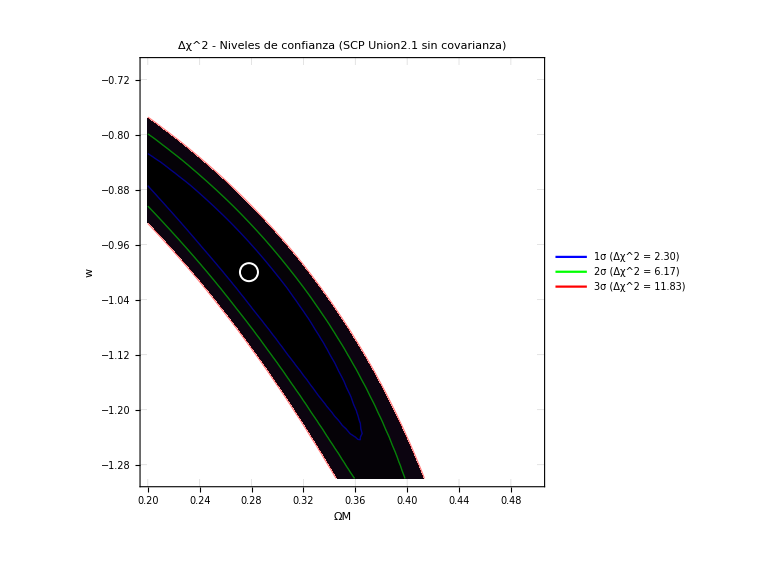

```mathematica
(*ANALISIS COSMOLOGICO-SCP UNION2.1*)(*w-CDM:distancia de luminosidad,chi2 y niveles confianza*)
Clear[muTeo,chi2]

OmegaM=0.3;
OmegaDE=0.7;
H0=70.0;
c=299792.458;

(*Lectura del dataset SCP Union2.1*)
dataRaw=Import["C:\\Users\\joses\\OneDrive\\Documents\\Mathematica\\SCPUnion2.1_mu_vs_z.txt","Table"];
zObs=dataRaw[[All,2]];(*redshift*)muObs=dataRaw[[All,3]];(*mu observado*)sigmaObs=dataRaw[[All,4]];(*error estadistico*)n=Length[zObs];
Print["Numero de supernovas: ",n]

(*BLOQUE 1:CALCULO DE MU TEORICO PARA 3 VALORES DE w*)

atable1=Table[{z,5*Log10[(1+z)*(c/H0)*NIntegrate[1/Sqrt[OmegaM*(1+zp)^3+OmegaDE*(1+zp)^(3*(1+(-1.0)))],{zp,0,z}]]+25},{z,0.001,2.5,0.001}];

atable2=Table[{z,5*Log10[(1+z)*(c/H0)*NIntegrate[1/Sqrt[OmegaM*(1+zp)^3+OmegaDE*(1+zp)^(3*(1+(-0.8)))],{zp,0,z}]]+25},{z,0.001,2.5,0.001}];

atable3=Table[{z,5*Log10[(1+z)*(c/H0)*NIntegrate[1/Sqrt[OmegaM*(1+zp)^3+OmegaDE*(1+zp)^(3*(1+(-1.2)))],{zp,0,z}]]+25},{z,0.001,2.5,0.001}];

Print["Primeros 10 valores de μ teorico (w = -1.0)"]
Print[TableForm[Take[atable1,10],TableHeadings->{None,{"z","μ"}}]]

(*BLOQUE 2:GRAFICAS CON EJE X LOGARITMICO*)

p1log=ListLinePlot[{atable1,atable2,atable3},PlotStyle->{{Blue,Thick},{Green,Thick},{Orange,Thick}},PlotLegends->{"w = -1.0","w = -0.8","w = -1.2"},FrameLabel->{{"μ",None},{"log10(z)",None}},PlotLabel->"Calculo teorico μ(z) - eje x logaritmico (SCP Union2.1)",Frame->True,GridLines->Automatic,ImageSize->Large,ScalingFunctions->{"Log10",None}];

puntoslog=ListPlot[{Log10[zObs[[i]]],muObs[[i]]}&/@Range[n],PlotStyle->{Red,PointSize[0.004]},ScalingFunctions->{"Log10",None}];

barraslog=Graphics[{Red,Thin,Table[Line[{{Log10[zObs[[i]]],muObs[[i]]-sigmaObs[[i]]},{Log10[zObs[[i]]],muObs[[i]]+sigmaObs[[i]]}}],{i,1,n}]}];

p2log=Show[puntoslog,barraslog,PlotRange->{{Log10[0.001],Log10[2.5]},{33,47}},FrameLabel->{{"μ",None},{"log10(z)",None}},PlotLabel->"SCP Union2.1: datos y barras de error - eje x logaritmico",Frame->True,GridLines->Automatic,ImageSize->Large];

p3log=Show[p1log,p2log,FrameLabel->{{"μ",None},{"log10(z)",None}},PlotLabel->"Teoria vs SCP Union2.1 - eje x logaritmico",ImageSize->Large];

Print["Figura 1: Curvas teoricas (eje x log)"]
p1log
Print["Figura 2: Datos con barras de error (eje x log)"]
p2log
Print["Figura 3: Superposicion teoria + datos (eje x log)"]
p3log

(*BLOQUE 3:GRAFICAS CON AMBOS EJES LOGARITMICOS*)

(*Pre-transformar a log10 en ambos ejes*)
atable1log={Log10[#[[1]]],Log10[#[[2]]]}&/@atable1;
atable2log={Log10[#[[1]]],Log10[#[[2]]]}&/@atable2;
atable3log={Log10[#[[1]]],Log10[#[[2]]]}&/@atable3;

p1loglog=ListLinePlot[{atable1log,atable2log,atable3log},PlotStyle->{{Blue,Thick},{Green,Thick},{Orange,Thick}},PlotLegends->{"w = -1.0","w = -0.8","w = -1.2"},FrameLabel->{{"log10(μ)",None},{"log10(z)",None}},PlotLabel->"Calculo teorico μ(z) - ambos ejes logaritmicos (SCP Union2.1)",Frame->True,GridLines->Automatic,ImageSize->Large];

puntosloglog=ListPlot[{Log10[zObs[[i]]],Log10[muObs[[i]]]}&/@Range[n],PlotStyle->{Red,PointSize[0.004]}];

barrasloglog=Graphics[{Red,Thin,Table[Line[{{Log10[zObs[[i]]],Log10[muObs[[i]]-sigmaObs[[i]]]},{Log10[zObs[[i]]],Log10[muObs[[i]]+sigmaObs[[i]]]}}],{i,1,n}]}];

p2loglog=Show[puntosloglog,barrasloglog,PlotRange->{{Log10[0.001],Log10[2.5]},{Log10[33],Log10[47]}},FrameLabel->{{"log10(μ)",None},{"log10(z)",None}},PlotLabel->"SCP Union2.1: datos y barras de error - ambos ejes logaritmicos",Frame->True,GridLines->Automatic,ImageSize->Large];

p3loglog=Show[p1loglog,p2loglog,FrameLabel->{{"log10(μ)",None},{"log10(z)",None}},PlotLabel->"Teoria vs SCP Union2.1 - ambos ejes logaritmicos",ImageSize->Large];

Print["Figura 4: Curvas teoricas (ambos ejes log)"]
p1loglog
Print["Figura 5: Datos con barras de error (ambos ejes log)"]
p2loglog
Print["Figura 6: Superposicion teoria + datos (ambos ejes log)"]
p3loglog

(*BLOQUE 4:CHI CUADRADO PARA LOS TRES VALORES DE w FIJO*)

chi2w1=Total[Table[Module[{muTeo},muTeo=5*Log10[(1+zObs[[i]])*(c/H0)*NIntegrate[1/Sqrt[OmegaM*(1+zp)^3+OmegaDE*(1+zp)^(3*(1+(-1.0)))],{zp,0,zObs[[i]]},AccuracyGoal->4,PrecisionGoal->4]]+25;
(muTeo-muObs[[i]])^2/sigmaObs[[i]]^2],{i,1,n}]];

chi2w2=Total[Table[Module[{muTeo},muTeo=5*Log10[(1+zObs[[i]])*(c/H0)*NIntegrate[1/Sqrt[OmegaM*(1+zp)^3+OmegaDE*(1+zp)^(3*(1+(-0.8)))],{zp,0,zObs[[i]]},AccuracyGoal->4,PrecisionGoal->4]]+25;
(muTeo-muObs[[i]])^2/sigmaObs[[i]]^2],{i,1,n}]];

chi2w3=Total[Table[Module[{muTeo},muTeo=5*Log10[(1+zObs[[i]])*(c/H0)*NIntegrate[1/Sqrt[OmegaM*(1+zp)^3+OmegaDE*(1+zp)^(3*(1+(-1.2)))],{zp,0,zObs[[i]]},AccuracyGoal->4,PrecisionGoal->4]]+25;
(muTeo-muObs[[i]])^2/sigmaObs[[i]]^2],{i,1,n}]];

Print["Chi cuadrado para w fijo"]
Print["Chi2 (w = -1.0) = ",chi2w1]
Print["Chi2 (w = -0.8) = ",chi2w2]
Print["Chi2 (w = -1.2) = ",chi2w3]

(*BLOQUE 5:BUCLE 2D EN (OmegaM,w) Y CONTOUR PLOT*)

Print["Calculando chi cuadrado en bucle 2D..."]
chiTable2D=Table[Module[{om=omVal,ode=1-omVal},chi2=Total[Table[Module[{muTeo},muTeo=5*Log10[(1+zObs[[i]])*(c/H0)*NIntegrate[1/Sqrt[om*(1+zp)^3+ode*(1+zp)^(3*(1+wVal))],{zp,0,zObs[[i]]},AccuracyGoal->4,PrecisionGoal->4]]+25;
(muTeo-muObs[[i]])^2/sigmaObs[[i]]^2],{i,1,n}]];
{omVal,wVal,1-omVal,chi2}],{omVal,0.2,0.5,0.006},{wVal,-1.3,-0.7,0.012}];

chiFlat=Flatten[chiTable2D,1];

(*Minimo global y delta chi cuadrado*)
minGlobal=MinimalBy[chiFlat,#[[4]]&][[1]];
Print["Minimo global: χ^2 = ",minGlobal[[4]]," en OmegaM = ",minGlobal[[1]],", w = ",minGlobal[[2]],", OmegaDE = ",minGlobal[[3]]]

chiMin=minGlobal[[4]];
chiDelta={#[[1]],#[[2]],#[[3]],#[[4]]-chiMin}&/@chiFlat;

(*Niveles de confianza*)
sigma1=Select[chiDelta,#[[4]]≤2.30&];
sigma2=Select[chiDelta,#[[4]]≤6.17&];
sigma3=Select[chiDelta,#[[4]]≤11.83&];
Print["Puntos dentro de 1σ: ",Length[sigma1]]
Print["Puntos dentro de 2σ: ",Length[sigma2]]
Print["Puntos dentro de 3σ: ",Length[sigma3]]

(*Contour plot:eje x=OmegaM,eje y=w*)
chiDeltaXY={#[[1]],#[[2]],#[[4]]}&/@chiDelta;

Print["Figura 7: Contour plot niveles de confianza"]
ListContourPlot[chiDeltaXY,Contours->{2.30,6.17,11.83},ContourStyle->{{Blue,Thick},{Green,Thick},{Red,Thick}},ColorFunction->"SunsetColors",ContourShading->True,FrameLabel->{{"w",None},{"ΩM",None}},PlotLabel->"Δχ^2 - Niveles de confianza (SCP Union2.1 sin covarianza)",PlotLegends->Placed[LineLegend[{Blue,Green,Red},{"1σ (Δχ^2 = 2.30)","2σ (Δχ^2 = 6.17)","3σ (Δχ^2 = 11.83)"}],Right],Epilog->{White,PointSize[0.025],Point[{minGlobal[[1]],minGlobal[[2]]}],Black,PointSize[0.02],Point[{minGlobal[[1]],minGlobal[[2]]}]},Frame->True,GridLines->Automatic,ImageSize->Large]
```